# Construction of the LS method for the Stochastic HIV Dynamics Model.

```mathematica
a:=0.5;
u:=5;
β:=10^(-8);
γ:=0.5;
η:=0.5;
NN:=100;
δ:=0.1;
λ:=10^6;

a1[{x_,y_,z_}]:=-δ-(1-γ)*β*z; 
a2[{x_,y_,z_}]:= -a;
a3[{x_,y_,z_}]:=-u -(1-γ)*β*x;
b1[{x_,y_,z_}]:=λ;
b2[{x_,y_,z_}]:=(1-γ)*β*x*z;
b3[{x_,y_,z_}]:= (1-η)*NN*a*y;
f1[{x_,y_,z_}]:= a1[{x,y,z}]*x+b1[{x,y,z}];
f2[{x_,y_,z_}]:= a2[{x,y,z}]*y+b2[{x,y,z}];
f3[{x_,y_,z_}]:= a3[{x,y,z}]*z+b3[{x,y,z}];
```

```mathematica
Fh1[{x_,y_,z_},ϵ_]:=x*Exp[ϵ*a1[{x,y,z}]]+b1[{x,y,z}]*(Exp[ϵ*a1[{x,y,z}]]-1)/a1[{x,y,z}];
Fh2[{x_,y_,z_},ϵ_]:=y*Exp[ϵ*a2[{x,y,z}]]+b2[{x,y,z}]*(Exp[-a*ϵ]-1)/-a;
Fh3[{x_,y_,z_},ϵ_]:=z*Exp[ϵ*a3[{x,y,z}]]+b3[{x,y,z}]*(Exp[ϵ*a3[{x,y,z}]]-1)/a3[{x,y,z}];
```

```mathematica
Ah[{x_,y_,z_},ϵ_]:=DiagonalMatrix[
{
Exp[ϵ*a1[{x,y,z}]],
Exp[ϵ*a2[{x,y,z}]],
Exp[ϵ*a3[{x,y,z}]]
}
](*//MatrixForm*)
```

```mathematica
Gh[{x_,y_,z_},ϵ_]:=DiagonalMatrix[
{
(Exp[ϵ*a1[{x,y,z}]]-1)/a1[{x,y,z}],
(Exp[ϵ*a2[{x,y,z}]]-1)/a2[{x,y,z}],
(Exp[ϵ*a3[{x,y,z}]]-1)/a3[{x,y,z}]
}
](*//MatrixForm*)
b[{x_,y_,z_}]:={b1[{x,y,z}],b2[{x,y,z}],b3[{x,y,z}]};
```

```mathematica
Ah[{x,y,z},.01].{x,y,z} +Gh[{x,y,z},.01].b[{x,y,z}]
```

{0.+ⅇ^(0.01 (-0.1-5.×10^-9 z)) x+(1000000 (-1+ⅇ^(0.01 (-0.1-5.×10^-9 z))))/(-0.1-5.×10^-9 z),0.+0.995012 y+4.98752×10^-11 x z,0.+(25. (-1+ⅇ^(0.01 (-5-5.×10^-9 x))) y)/(-5-5.×10^-9 x)+ⅇ^(0.01 (-5-5.×10^-9 x)) z}

```mathematica
NFh[{x_,y_,z_},ϵ_]:=
Norm[
Ah[{x,y,z},.01].{x,y,z} +Gh[{x,y,z},.01].b[{x,y,z}]
];

Plot3D[NFh[{100,y,z},.01],{y,0,100},{z,0,100},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

```mathematica
DensityPlot[NFh[{10000,y,z},.01],{y,0,100000},{z,0,100000},ColorFunction->"BlueGreenYellow"]
```

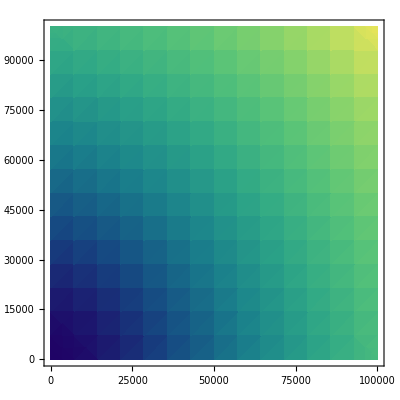

```mathematica
Element[x,Reals];
Element[y,Reals];
Element[z,Reals];
{U1,S1,V1}=SingularValueDecomposition[Ah[{x,y,z},.1]];
{U2,S2,V2}=SingularValueDecomposition[Gh[{x,y,z},.1]];
(*U //MatrixForm*)
Refine[S1,Assumptions->{Element[x,Reals],Element[y,Reals],Element[z,Reals]} ]//MatrixForm
Refine[S2,Assumptions->{Element[x,Reals],Element[y,Reals],Element[z,Reals]} ]//MatrixForm
(*Transpose[V] //MatrixForm*)
```

(0.951229 | 0 | 0
0 | √(0.+ⅇ^(0.2 (-5-5.×10^-9 x))) | 0
0 | 0 | √(0.+ⅇ^(0.2 (-0.1-5.×10^-9 z))))

1. ⅇ^(5.×10^-10 x+5.×10^-10 z) √(ⅇ^(-1.×10^-9 x)) √(ⅇ^(-1.×10^-9 z))

(0.0975412 | 0 | 0
0 | √(0.+((-1+ⅇ^(0.1 (-5-5.×10^-9 x)))^2)/((-5-5.×10^-9 x)^2)) | 0
0 | 0 | √(0.+((-1+ⅇ^(0.1 (-0.1-5.×10^-9 z)))^2)/((-0.1-5.×10^-9 z)^2)))

```mathematica
Limit[√(((-1+ⅇ^(0.1 (-5-5.*^-9 x)))^2)/((-5-5.*^-9 x)^2)),x->0]
```

0.0786939